Images created for “What are the proposed realizations in the New SI for the kilogram, ampere, kelvin and mole?” at  http://physics.stackexchange.com/q/147433, and “Proposed redefinition of SI base units” at https://en.wikipedia.org/wiki/Proposed_redefinition_of_SI_base_units.

© Emilio Pisanty, 2016, made available under the CC BY-SA 4.0 licence.

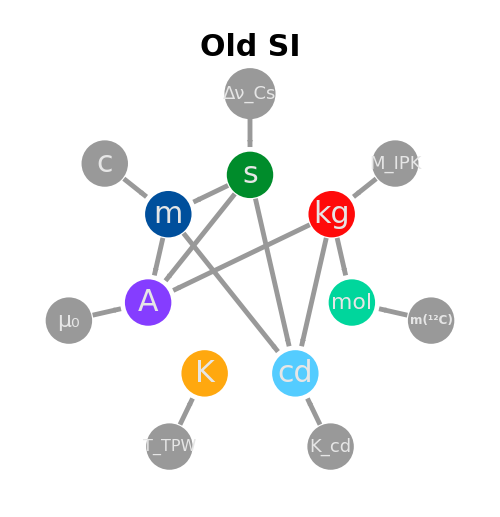

```mathematica
fs=30;
fs2=25;
φ=2π/7;
p[n_]:=4.5{Sin[n φ],Cos[n φ]}
q[n_]:=8{Sin[n φ],Cos[n φ]}
oldSI=Show[{
Graphics[{RGBColor[0., 0.55, 0.17],Disk[p[0],1]}],
Graphics[{Text[Style["s",fs,GrayLevel[0.9]],p[0]]}],
Graphics[{RGBColor[1., 0.04, 0.04],Disk[p[1],1]}],
Graphics[{Text[Style["kg",fs,GrayLevel[0.9]],p[1]]}],
Graphics[{RGBColor[0., 0.84, 0.61],Disk[p[2],1]}],
Graphics[{Text[Style["mol",fs-8,GrayLevel[0.9]],p[2]]}],
Graphics[{RGBColor[0.33, 0.8, 1.],Disk[p[3],1]}],
Graphics[{Text[Style["cd",fs,GrayLevel[0.9]],p[3]]}],
Graphics[{RGBColor[1., 0.66, 0.06],Disk[p[4],1]}],
Graphics[{Text[Style["K",fs,GrayLevel[0.9]],p[4]]}],
Graphics[{RGBColor[0.52, 0.24, 1.],Disk[p[5],1]}],
Graphics[{Text[Style["A",fs,GrayLevel[0.9]],p[5]]}],
Graphics[{RGBColor[0., 0.31, 0.61],Disk[p[6],1]}],
Graphics[{Text[Style["m",fs,GrayLevel[0.9]],p[6]]}],

Graphics[{GrayLevel[0.6],Disk[q[0],1.1]}],
Graphics[{Text[Style["Δν_Cs",18,GrayLevel[0.9]],q[0]]}],
Graphics[{GrayLevel[0.6],Disk[q[1],1]}],
Graphics[{Text[Style["M_IPK",18,GrayLevel[0.9]],q[1]]}],
Graphics[{GrayLevel[0.6],Disk[q[2],1]}],
Graphics[{Text[Style["m(^12C)",12,Bold,GrayLevel[0.9]],q[2]]}],
Graphics[{GrayLevel[0.6],Disk[q[3],1]}],
Graphics[{Text[Style["K_cd",18,GrayLevel[0.9]],q[3]]}],
Graphics[{GrayLevel[0.6],Disk[q[4],1]}],
Graphics[{Text[Style["T_TPW",16,GrayLevel[0.9]],q[4]]}],
Graphics[{GrayLevel[0.6],Disk[q[5],1]}],
Graphics[{Text[Style["μ_0",22,GrayLevel[0.9]],q[5]]}],
Graphics[{GrayLevel[0.6],Disk[q[6],1]}],
Graphics[{Text[Style["c",30,Italic,GrayLevel[0.9]],q[6]]}],

Graphics[{
h=Graphics[{Thickness[0.007],Line[0.5{{-1,1/2},{0,0},{-1,-1/2}}]}];
Thickness[0.007],Arrowheads[{{0.05,1,h}}],GrayLevel[0.6],
Arrow[{p[0],p[6]},{1.05,1.2}],
Arrow[{p[0],p[3]},{1.05,1.2}],
Arrow[{p[0],p[5]},{1.05,1.2}],
Arrow[{p[6],p[3]},{1.05,1.2}],
Arrow[{p[6],p[5]},{1.05,1.2}],
Arrow[{p[1],p[2]},{1.05,1.2}],
Arrow[{p[1],p[3]},{1.05,1.2}],
Arrow[{p[1],p[5]},{1.05,1.2}]
}~Join~(
Arrow[{q[#],p[#]},{1.05,1.2}]&/@Range[0,6]
)],
Graphics[Text[Style["Old SI",Bold,30],{0,10}]]
}
,ImageSize->500
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Unit relations in the old SI.svg"}],oldSI];
```

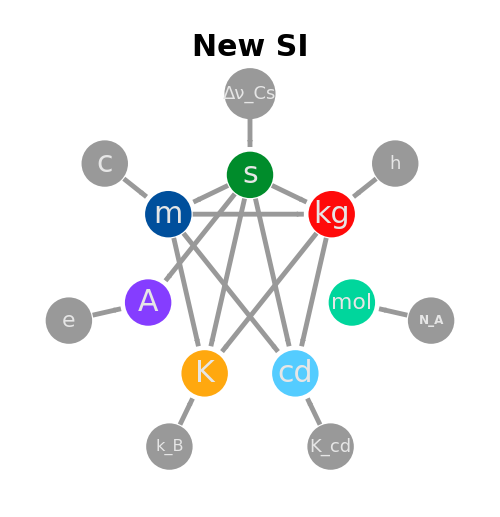

```mathematica
fs=30;
fs2=25;
φ=2π/7;
p[n_]:=4.5{Sin[n φ],Cos[n φ]}
q[n_]:=8{Sin[n φ],Cos[n φ]}
newSI=Show[{
Graphics[{RGBColor[0., 0.55, 0.17],Disk[p[0],1]}],
Graphics[{Text[Style["s",fs,GrayLevel[0.9]],p[0]]}],
Graphics[{RGBColor[1., 0.04, 0.04],Disk[p[1],1]}],
Graphics[{Text[Style["kg",fs,GrayLevel[0.9]],p[1]]}],
Graphics[{RGBColor[0., 0.84, 0.61],Disk[p[2],1]}],
Graphics[{Text[Style["mol",fs-8,GrayLevel[0.9]],p[2]]}],
Graphics[{RGBColor[0.33, 0.8, 1.],Disk[p[3],1]}],
Graphics[{Text[Style["cd",fs,GrayLevel[0.9]],p[3]]}],
Graphics[{RGBColor[1., 0.66, 0.06],Disk[p[4],1]}],
Graphics[{Text[Style["K",fs,GrayLevel[0.9]],p[4]]}],
Graphics[{RGBColor[0.52, 0.24, 1.],Disk[p[5],1]}],
Graphics[{Text[Style["A",fs,GrayLevel[0.9]],p[5]]}],
Graphics[{RGBColor[0., 0.31, 0.61],Disk[p[6],1]}],
Graphics[{Text[Style["m",fs,GrayLevel[0.9]],p[6]]}],

Graphics[{GrayLevel[0.6],Disk[q[0],1.1]}],
Graphics[{Text[Style["Δν_Cs",18,GrayLevel[0.9]],q[0]]}],
Graphics[{GrayLevel[0.6],Disk[q[1],1]}],
Graphics[{Text[Style["h",Italic,18,GrayLevel[0.9]],q[1]]}],
Graphics[{GrayLevel[0.6],Disk[q[2],1]}],
Graphics[{Text[Style["N_A",12,Bold,GrayLevel[0.9]],q[2]]}],
Graphics[{GrayLevel[0.6],Disk[q[3],1]}],
Graphics[{Text[Style["K_cd",18,GrayLevel[0.9]],q[3]]}],
Graphics[{GrayLevel[0.6],Disk[q[4],1]}],
Graphics[{Text[Style["k_B",16,GrayLevel[0.9]],q[4]]}],
Graphics[{GrayLevel[0.6],Disk[q[5],1]}],
Graphics[{Text[Style["e",Italic,22,GrayLevel[0.9]],q[5]]}],
Graphics[{GrayLevel[0.6],Disk[q[6],1]}],
Graphics[{Text[Style["c",Italic,30,GrayLevel[0.9]],q[6]]}],

Graphics[{
h=Graphics[{Thickness[0.007],Line[0.5{{-1,1/2},{0,0},{-1,-1/2}}]}];
Thickness[0.007],Arrowheads[{{0.05,1,h}}],GrayLevel[0.6],
Arrow[{p[0],p[1]},{1.05,1.2}],
Arrow[{p[0],p[3]},{1.05,1.2}],
Arrow[{p[0],p[4]},{1.05,1.2}],
Arrow[{p[0],p[5]},{1.05,1.2}],
Arrow[{p[0],p[6]},{1.05,1.2}],
Arrow[{p[1],p[3]},{1.05,1.2}],
Arrow[{p[1],p[4]},{1.05,1.2}],
Arrow[{p[6],p[1]},{1.05,1.2}],
Arrow[{p[6],p[3]},{1.05,1.2}],
Arrow[{p[6],p[4]},{1.05,1.2}]
}~Join~(
Arrow[{q[#],p[#]},{1.05,1.2}]&/@Range[0,6]
)],
Graphics[Text[Style["New SI",Bold,30],{0,10}]]
}
,ImageSize->500
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Unit relations in the new SI.svg"}],newSI];
```